```mathematica
Quiet@Needs["MagneticTB`"];
```

```mathematica
SystemOpen[FileNameJoin[{$UserBaseDirectory,"Applications"}]]
```

## Construct TB Model

```mathematica
sgop=msgop[gray[156]];
init[lattice->{{a,0,0},{-(a/2),(Sqrt[3] a)/2,0},{0,0,c}},
lattpar->{a->1,c->10},
wyckoffposition->{{{2/3,1/3,0},{0,0,0}}},
symminformation->sgop,
basisFunctions->{{"dz2","dxy","dx2-y2"}}];
```

Magnetic space group (BNS): {156.50,P3m11'}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

```mathematica
ham=Sum[symham[n,symmetryset->(*All*)  {6,2}],{n,1,2}];MatrixForm[ham]
```

params:{e1,e2}

params:{t1,t2,t3,t4,t5,t6,t7,t8,t9}

(e1+ⅇ^(-ⅈ kx) t4+ⅇ^(ⅈ kx) t4+ⅇ^(ⅈ (-kx-ky)) t4+ⅇ^(-ⅈ ky) t4+ⅇ^(ⅈ ky) t4+ⅇ^(ⅈ (kx+ky)) t4 | ⅇ^(ⅈ ky) (ⅈ t1-t5)+ⅇ^(ⅈ (kx+ky)) (-ⅈ t1+t5)+ⅇ^(-ⅈ kx) (1/2 ⅈ (t1+√3 t2)+1/2 (-t5-√3 t7))+ⅇ^(ⅈ (-kx-ky)) (1/2 ⅈ (-t1+√3 t2)+1/2 (t5-√3 t7))+ⅇ^(-ⅈ ky) (1/2 ⅈ (t1-√3 t2)+1/2 (-t5+√3 t7))+ⅇ^(ⅈ kx) (-1/2 ⅈ (t1+√3 t2)+1/2 (t5+√3 t7)) | ⅇ^(ⅈ (-kx-ky)) (1/2 ⅈ (√3 t1+t2)+1/2 (-√3 t5-t7))+ⅇ^(-ⅈ ky) (1/2 ⅈ (√3 t1+t2)+1/2 (-√3 t5-t7))+ⅇ^(ⅈ kx) (-1/2 ⅈ (√3 t1-t2)+1/2 (√3 t5-t7))+ⅇ^(-ⅈ kx) (1/2 ⅈ (-√3 t1+t2)+1/2 (√3 t5-t7))+ⅇ^(ⅈ ky) (-ⅈ t2+t7)+ⅇ^(ⅈ (kx+ky)) (-ⅈ t2+t7)
ⅇ^(-ⅈ ky) (-ⅈ t1-t5)+ⅇ^(ⅈ (-kx-ky)) (ⅈ t1+t5)+ⅇ^(ⅈ kx) (-1/2 ⅈ (t1+√3 t2)+1/2 (-t5-√3 t7))+ⅇ^(ⅈ (kx+ky)) (-1/2 ⅈ (-t1+√3 t2)+1/2 (t5-√3 t7))+ⅇ^(ⅈ ky) (-1/2 ⅈ (t1-√3 t2)+1/2 (-t5+√3 t7))+ⅇ^(-ⅈ kx) (1/2 ⅈ (t1+√3 t2)+1/2 (t5+√3 t7)) | e2+ⅇ^(ⅈ (-kx-ky)) (-ⅈ t3-t6/(√3)-t8/(√3)+t9)+ⅇ^(-ⅈ ky) (-ⅈ t3-t6/(√3)-t8/(√3)+t9)+ⅇ^(ⅈ ky) (ⅈ t3-t6/(√3)-t8/(√3)+t9)+ⅇ^(ⅈ (kx+ky)) (ⅈ t3-t6/(√3)-t8/(√3)+t9)+1/6 ⅇ^(-ⅈ kx) (√3 t6+√3 t8+6 t9)+1/6 ⅇ^(ⅈ kx) (√3 t6+√3 t8+6 t9) | ⅇ^(-ⅈ ky) ((ⅈ t3)/(√3)-t6)+ⅇ^(ⅈ (-kx-ky)) (-(ⅈ t3)/(√3)+t6)+ⅇ^(ⅈ kx) ((2 ⅈ t3)/(√3)+(t6-t8)/2)+ⅇ^(ⅈ ky) (-(ⅈ t3)/(√3)-t8)+ⅇ^(ⅈ (kx+ky)) ((ⅈ t3)/(√3)+t8)+ⅇ^(-ⅈ kx) (-(2 ⅈ t3)/(√3)+1/2 (-t6+t8))
ⅇ^(ⅈ ky) (-1/2 ⅈ (√3 t1+t2)+1/2 (-√3 t5-t7))+ⅇ^(ⅈ (kx+ky)) (-1/2 ⅈ (√3 t1+t2)+1/2 (-√3 t5-t7))+ⅇ^(-ⅈ kx) (1/2 ⅈ (√3 t1-t2)+1/2 (√3 t5-t7))+ⅇ^(ⅈ kx) (-1/2 ⅈ (-√3 t1+t2)+1/2 (√3 t5-t7))+ⅇ^(ⅈ (-kx-ky)) (ⅈ t2+t7)+ⅇ^(-ⅈ ky) (ⅈ t2+t7) | ⅇ^(ⅈ ky) (-(ⅈ t3)/(√3)-t6)+ⅇ^(ⅈ (kx+ky)) ((ⅈ t3)/(√3)+t6)+ⅇ^(-ⅈ kx) (-(2 ⅈ t3)/(√3)+(t6-t8)/2)+ⅇ^(-ⅈ ky) ((ⅈ t3)/(√3)-t8)+ⅇ^(ⅈ (-kx-ky)) (-(ⅈ t3)/(√3)+t8)+ⅇ^(ⅈ kx) ((2 ⅈ t3)/(√3)+1/2 (-t6+t8)) | e2+ⅇ^(ⅈ ky) (-ⅈ t3+t9)+ⅇ^(ⅈ (kx+ky)) (-ⅈ t3+t9)+ⅇ^(ⅈ (-kx-ky)) (ⅈ t3+t9)+ⅇ^(-ⅈ ky) (ⅈ t3+t9)+ⅇ^(-ⅈ kx) (-(√3 t6)/2-(√3 t8)/2+t9)+ⅇ^(ⅈ kx) (-(√3 t6)/2-(√3 t8)/2+t9))

## Obtain the TB parameters by hand

#### vaspEig[filename_,Fermienergy_,spin,bandstart_,bandend_] filename is the EIGENVAL calculated by VASP Fermienergy is the value of Fermi energy spin is the spin component (1 for up and 2 for down). Notice when SOC is considered spin is always set as 1 bandstart and bandend is the band index form bandstart to bandend one want to consider

### Step I read the vasp EIGENVAL and KPOINT file

```mathematica
eigdata=vaspEig[NotebookDirectory[]<>"EIGENVAL",-0.0072,1,21,23];
pathstr="0.0 0.0 0.0 ! \\Gamma
0.5 0.0 0.0 ! M

0.5 0.0 0.0 ! M
0.3333333333333333 0.3333333333333333 0.0 ! K

0.3333333333333333 0.3333333333333333 0.0 ! K
0.0 0.0 0.0 ! \\Gamma";
klist=tokpathvasp[pathstr,30];
vasptoPath={Rationalize[ToExpression@Partition[Partition[StringSplit[#],5][[;;,{1,2,3}]],2]],Partition[Partition[StringSplit[#],5][[;;,-1]],2]}ᵀ&;
path=vasptoPath@pathstr;
```

### Step II Adjustment the parameters by hand

```mathematica
bandManipulateEig[ham,klist,eigdata]
```

Number of params:11

params:{e1,e2,t1,t2,t3,t4,t5,t6,t7,t8,t9}

mparams:{pe1,pe2,pt1,pt2,pt3,pt4,pt5,pt6,pt7,pt8,pt9}

### Step III Plot the band structure

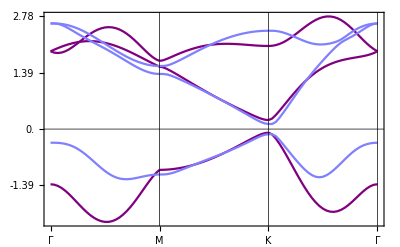
-Graphics-Red: TB, Blue: VASP

```mathematica
compareBand[path,30,ham,{e1->0.915,e2->0.685,t1->0.10000000000000009,t2->0.09000000000000008,t3->0.10000000000000009,t4->-0.38,t5->0.3400000000000001,t6->0.2450000000000001,t7->0.565,t8->0.30499999999999994,t9->0.365},eigdata]
```